The governing equation is (∂T)/(∂t)=α((∂^2 T)/(∂x^2)+(∂^2 T)/(∂y^2)) and for steady state, we have (∂T)/(∂t)=0

```mathematica
nx=21; ny=21;
Δx=1/(nx-1); Δy=1/(ny-1);
k=1; h=10; Subscript[T, 0]=300; Subscript[T, left] = 350; α=1;
u = 1; v=2;
T = Array["T",{nx,ny}];
```

```mathematica
discreteEqns = Table[
u (T[[i,j]]-T[[i-1,j]])/Δx+v (T[[i,j]]-T[[i,j-1]])/Δy==α((T[[i+1,j]]-2T[[i,j]]+T[[i-1,j]])/Δx^2+(T[[i,j+1]]-2T[[i,j]]+T[[i,j-1]])/Δy^2),
{i,2,nx-1},{j,2,ny-1}];
```

```mathematica
leftBoundary = Table[T[[1,j]]==Subscript[T, left],{j,2,ny-1}];
topBoundary = Table[T[[i,ny]]==T[[i,ny-1]],{i,1,nx}];
bottomBoundary = Table[T[[i,1]]==280,{i,1,nx}];
rightBoundary = Table[-k/Δx(T[[nx,j]]-T[[nx-1,j]])==h(T[[nx,j]]-Subscript[T, 0]),{j,2,ny-1}];
```

```mathematica
eqns = Join[Flatten[discreteEqns],leftBoundary,topBoundary,rightBoundary,bottomBoundary];
```

```mathematica
sol = NSolve[eqns,Flatten[T]];
```

```mathematica
TVals = T/.sol // #[[1]]&;
```

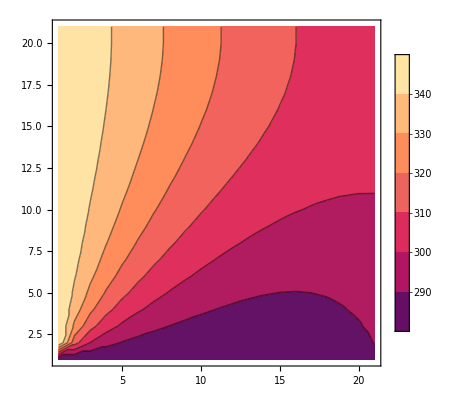

```mathematica
ListContourPlot[Transpose[TVals],PlotLegends->Automatic]
```